```mathematica
ClearAll["Global`*"]
```

```mathematica
read[name_]:=Flatten[Import[name,"Table"]];
files=FileNames["*.bin",NotebookDirectory[]];
Do[Print[files[[i]]],{i,1,Length[files]}]
```

/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/128Te/ENER.bin

/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/128Te/ENER-Te128-BM.bin

/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/128Te/STRE.bin

/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/128Te/STRE-Te128-BM.bin

```mathematica
energyExp=read[files[[1]]];
energyTh=read[files[[2]]];
strengthEx=read[files[[3]]];
strengthTh=read[files[[4]]];
makedata[x_,y_]:=Table[{x[[i]],y[[i]]},{i,1,Length[x]}];
isotope=Row[{Superscript["","128"],"Te"}];
```

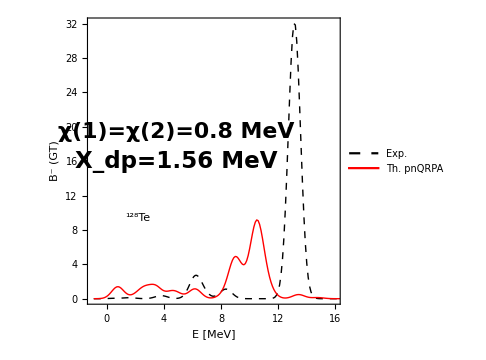

```mathematica
fig1=ListPlot[{makedata[energyExp,strengthEx],makedata[energyTh,strengthTh]},Joined->True,ImageSize->Medium,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E [MeV]","B^- (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"Exp.","Th. pnQRPA"},{0.4,0.8}],Epilog->{Inset[Style["χ(1)=χ(2)=0.8 MeV",22,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.6}]],Inset[Style["X_dp=1.56 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.35,0.5}]],Inset[Framed[Style[isotope,23,Bold,Black,FontFamily->"Times"]],Scaled[{0.2,0.3}]]},PlotStyle->{{Black,Dashed,Thick},{Red,Thick}},PlotRange->{{-1,16},Full}];
Show[fig1]
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA-double-beta-new-exp-data/128Te/STRE-BM-128Te.pdf",Show[fig1],ImageResolution->1200];
```